# Defining functions

Math 213 - Math with Mathematica
Christopher Hanusa

## Overview

In this tutorial, we learn how Mathematica defines named and unnamed functions.  By the end of this tutorial, you should be able to use Mathematica to define simple and complex functions for one or more inputs.

## Important Concept: Q

The computer can determine if the number you give it is even or odd.  
The command EvenQ is one of many Mathematica functions that ask a question (Q).  When you evaluate a number, EvenQ determines if the number is even or not.  Evaluate the next cell.

```mathematica
EvenQ[3]
EvenQ[4]
EvenQ[Sqrt[2]]
```

The command PrimeQ determines if a number is prime.  Evalulate the next cell.

```mathematica
PrimeQ[1]
PrimeQ[55]
PrimeQ[97]
PrimeQ[1234577]
```

Go to the Documentation Center and search for `Q' and focus on the built-in commands that end in Q, especially on the second page of results.  You will get a good feel for all the sorts of questions you can ask Mathematica to determine if a variable satisfies a property or not.

## Important Concept: If

It is often the case that you will want a function to do two things depending on whether a certain condition is true or false.  We will use the command If to do this.  The syntax for If is:

```mathematica
?If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

That is, you type If[condition,expression1,expression2], and Mathematica will first check the condition.  If the condition is True, then it will do expression1; otherwise it will do expression2.

```mathematica
z=10;
If[z^2<50,Print["z is small"],Print["z is large"]]
z=7;
If[z^2<50,Print["z is small"],Print["z is large"]]
```

### ! means negation

To change True to False or vice versa, use the ! operator.

```mathematica
!True
!False
!PrimeQ[77]
```

## Comprehension Questions

### 1. Look at the following commands. Before you evaluate each of them, determine what you think the output of each of these commands will be. Then evaluate each command and see if you were correct. If you were incorrect, then ask a classmate and discuss.

```mathematica
If[True,3,5]
```

```mathematica
If[IntegerQ[Pi],4,100]
```

```mathematica
Table[!OddQ[n],{n,1,10}]
```

```mathematica
Table[If[PrimeQ[n],1,0],{n,1,10}]
```

```mathematica
Table[If[PrimeQ[n],Print[n]],{n,1,10}];
```

## Defining a named function

f[x_,y_] := RHS

(RHS stands for Right Hand Side.)

f is the coder-specified name of the function.  Since all built-in Mathematica functions start with a capital letter, it’s good practice to start user-defined functions with a lower case letter.  To use multiple-word function names, captialize it #likeAHashtag.

All functions use square brackets [] to mark the beginning and end of the inputs.

Inside the square brackets, you give coder-specified names to each of the variables since you will be using them on the Right Hand Side of the definition when you code what the function does.

When you define these variables, use an underscore _ to tell Mathematica that the input for this variable can be any one thing. (One number, One list, One shape, ... anything!)  This is the simplest type of a “pattern” in Mathematica. We will learn more about patterns in the next tutorial.

Unlike defining variables and using the = operator, when you define a function you use the := operator.  It is called “SetDelayed” because it means that every time you evaluate the left hand side (When you call the function), it RE-evaluates the Right Hand Side.

### Simple function example

Define a function that takes as an input a number and outputs its square.

```mathematica
squareMe[x_]:=x^2
```

```mathematica
squareMe[-6]
```

36

Notice that Mathematica colors the coder-defined variables in the definition green. If you had made a mistake and not included the underscore, the color would be different:

```mathematica
squareMe[x]:=x^2
```

### Simple function with more than one variable

Define a function that takes as an input two numbers and outputs its sum.

```mathematica
addEmUp[x_,y_]:=x+y
```

```mathematica
addEmUp[3,-10]
```

-7

Notice that we did not specify that x and y had to be numbers.  Mathematica will add together whatever you put as inputs, even if the sum can’t be simplified.

```mathematica
addEmUp[{2,3},{9,-10}]
```

{11,-7}

```mathematica
addEmUp[Red,Orange]
```

RGBColor[1, 0, 0]+RGBColor[1, 0.5, 0]

```mathematica
addEmUp["Hello","Goodbye"]
```

Goodbye+Hello

### More information: Set vs. Set Delayed

Compare the following two lines of code:

```mathematica
x1=RandomInteger[{1,10}];
x2:=RandomInteger[{1,10}];
```

Notice that x1 is defined using Set (=) and x2 is defined using SetDelayed (:=).  This means that each time x1 is called, it will give the same random integer between 1 and 10, while each time x2 is called, it will give a new random integer between 1 and 10.

```mathematica
Table[x1,{10}]
Table[x2,{10}]
```

{9,9,9,9,9,9,9,9,9,9}

{10,5,9,3,7,8,5,9,6,4}

## Comprehension Questions

### 2. Define a function that takes as an input a number and outputs that number plus a random integer between 1 and 5.

### 3. Define a function abs that gives the absolute value of an input.

#### Hint (expand to see)

Use an If statement.

### 4. Define the function txp that takes as input an integer x and then outputs one of two things. If x is even, then output x/2. If x is odd, then output 3x+1.

### 5. What is wrong with the following code? It is supposed to take in a number, divide by two, then give the floor of that number. For example, the output for an input of 19 should be Floor[19/2]=Floor[9.5]=9.

```mathematica
fountainOfYouth[x]:=Floor[x/2]
fountainOfYouth(19)
```

## Defining an unnamed function

Let’s learn a more advanced way to define functions

Before we do that, let’s look at the internal format in which Mathematica defines a function.

### Using Function

Instead of defining our “square” and “addEmUp” functions like above, we could have instead written

```mathematica
alternateSquare:=Function[x,x^2]
```

```mathematica
alternateSquare[20]
```

400

```mathematica
alternateAddEmUp:=Function[{x,y},x+y]
```

```mathematica
alternateAddEmUp[-Pi,3Pi]
```

2 π

Here, we are using the Function command, which has two inputs.  The first input to Function is the input variable to the function (or list of input variables), and the second input to Function is the coder-defined output of the function.

### Unnamed functions

Suppose you want to code in a function that you only want to apply once and you don’t want to worry about giving it a name.  Then you can create an unnamed function.  They are a bit confusing at first, but become very handy as you become proficient.

(RHS(#))&   or   (RHS(#1,#2))&

(Again, RHS stands for Right Hand Side, and represents the actual function you want to apply to the variables.)

The # symbol represents an unnamed input variable.  While before you would define your right hand side around the input variable x, here wherever you would put x, you replace it by a # symbol. If your function has  more than one input, use #1, #2, #3, ... to represent the first, second, third, ... inputs in order.

The & symbol represents the end of the function and that signals to Mathematica that what follows should be the inputs to the function.

Often to increase readability, you can use parentheses ( ) to delimit the beginning and end of your unnamed function.

### Examples

The unnamed versions of the above functions are

```mathematica
#^2&
```

```mathematica
(#^2)&[Pi]
```

π^2

```mathematica
(#1+#2)&[3,4]
```

7

Notice that when calling unnamed functions, you still need to use square brackets around the inputs.

### Unnamed functions and Map

An especially handy place to use unnamed functions is in tandem with the Map command. You might have a list of objects and want to apply a function to the whole list, but don’t especially want to define the function outright.  You can use the Map command and an unnamed function to do it!

Here is an example that squares all the entries in a list.

```mathematica
mylist=Range[4,20,3]
Map[#^2&,mylist]
```

{4,7,10,13,16,19}

{16,49,100,169,256,361}

And here is an example that creates regular polygons with the number of sides of the entries in the list.


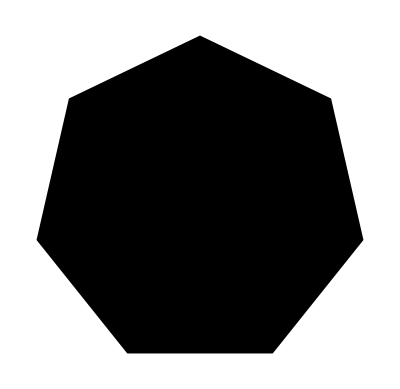
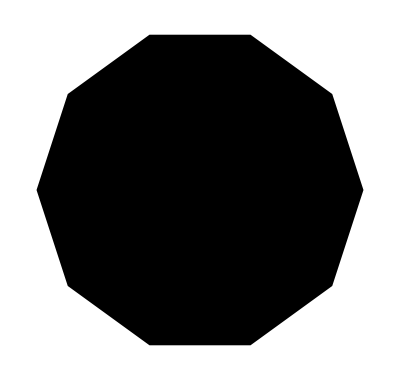
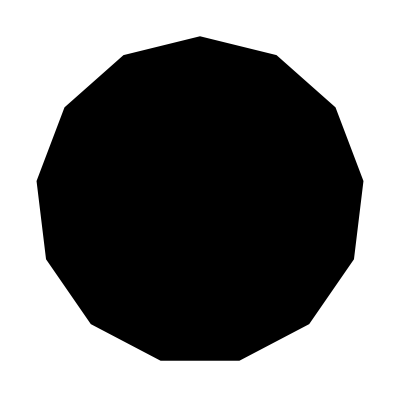
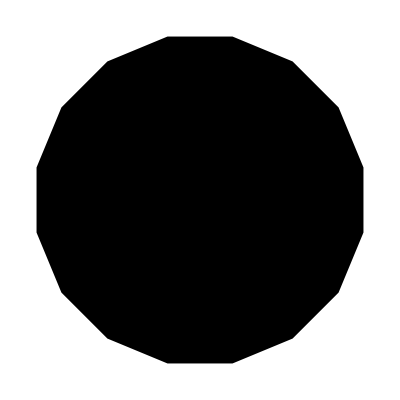
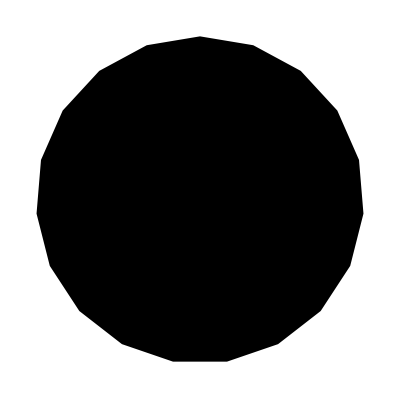

```mathematica
Map[Graphics[RegularPolygon[#]]&, mylist]
```

## Comprehension Questions

### 6. Create the unnamed function that does what fountainOfYouth was supposed to do in Question 5. Then use Map to apply that function to the list of integers from 1 to 20 (Use the Range command to generate that list).

### 7. Create an unnamed function that takes in three inputs and outputs one list with all three inputs in reverse order. (So for inputs 1, 4, 10, the output would be {10,4,1}.)

## Nest and NestList

If you want to apply a function multiple times, use the Nest command.  If you want to see the intermediate results of applying a function multiple times, use the NestList command.

```mathematica
?Nest
?NestList
```

RowBox[{"Nest", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives an expression with StyleBox["f", "TI"] applied StyleBox["n", "TI"] times to StyleBox["expr", "TI"].

NestList[f,expr,n] gives a list of the results of applying f to expr 0 through n times.

Here is an example that uses the function “subtract one”, and applies it to the input 100 four times in a row.  When you do this, you get the final answer 96, because
subtractOne[subtractOne[subtractOne[subtractOne[100]]]]=((((100-1)-1)-1)-1)=96.

```mathematica
subtractOne[x_]:=x-1
Nest[subtractOne,100,4]
```

96

But perhaps you wanted to know all the intermediate results.  Then use NestList to see the initial input, and the four steps.

```mathematica
NestList[subtractOne,100,4]
```

{100,99,98,97,96}

## Comprehension Questions

### 8. Rewrite the code that applies the “subtract one” command so that it uses an unnamed function instead of a named function.

### 9. Use a NestList command to apply the txp function from Question 4 twenty times. Try it on different integers and see what patterns arise.

## Important Concept: Module

When you are creating more complicated functions, you will need to use the Module function.

```mathematica
?Module
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

As you can see in the explanation of Module, it helps to quarantine the variables that you only use in this function.  This type of variables are called local variables.  As you can see in the following computation, even if i is defined outside the Module, you can use i inside without worrying about contamination.  It is good practice to define your functions in such a way that any variables you only use in your function are defined as local variables.

```mathematica
i=10;
Print["Outside Module, i is ",i]
Module[{i=20},Print["Inside Module, i is ",i]]
Print["Outside Module, i is ",i]
```

More importantly, Module lets you define a function that runs multiple lines of code in a row instead of just one line of code.  Each of these intermediate lines of code must end with a semicolon so that the each line of code is computed independently.  The output from the last line of code is the output of the whole Module command.

Here is an example that takes in two inputs, multiplies them together, then checks to see if this product is even or odd.  If the product is even, it divides by two.  If the product is odd, it subtracts one and then divides by two.  Then it checks to see if this result is prime or not, and displays either “Yay!” or “Bzzzz!”.  The output of this function is the list of the first result, second result, and third result.

```mathematica
manySteps[{x_,y_}]:=
 Module[{first,second,third},
first=x*y;
second=If[EvenQ[first],first/2,(first-1)/2];
third=If[PrimeQ[second],"Yay!","Bzzzz!"];
{first,second,third}]
```

Here are some examples of the results of this function, which you can check:

```mathematica
manySteps[{2,5}]
```

{10,5,Yay!}

```mathematica
manySteps[{3,5}]
```

{15,7,Yay!}

```mathematica
manySteps[{7,6}]
```

{42,21,Bzzzz!}

## Comprehension Questions

### 10. Create a Manipulate command that has the user modify the inputs to the manySteps function and dynamically updates the output.